```mathematica
BB[1]=({{0, 0, 0}, {0, 0, 1/(√2)}, {0, 1/(√2), 0}});  
 BB[2]=({{0, 0, 1/(√2)}, {0, 0, 0}, {1/(√2), 0, 0}});
BB[3]=({{0, 1/(√2), 0}, {1/(√2), 0, 0}, {0, 0, 0}});
BB[4]=({{-1/(√2), 0, 0}, {0, 1/(√2), 0}, {0, 0, 0}});BB[5]=1/(√6)({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}}); BB[6]=1/(√3)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
xyzTP[{θ_,ϕ_}]:={Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]};
InnerProductMatrix[M_,N_]:=Flatten[M].Flatten[N];
NormMatrix[M_]:=√InnerProductMatrix[M,M];
YRot[t_]:=({{Cos[t], 0, Sin[t]}, {0, 1, 0}, {-Sin[t], 0, Cos[t]}});
ZRot[t_]:=({{Cos[t], -Sin[t], 0}, {Sin[t], Cos[t], 0}, {0, 0, 1}});
id=IdentityMatrix[3];
matrixL[L_]:=Table[InnerProductMatrix[L[BB[j]],BB[i]],{i,6},{j,6}]; 
MatrixUbar[U_]:=matrixL[U.#.Transpose[U]&];  
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,MONO]:=({{a, g, 0, 0, 0, 0}, {g, b, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}})   (* This is P(T,Subscript[V, MONO](I)) in the 2022 paper *);
ProjToVSigOfU[Tmat_,U_,Σ_]:=MatrixUbar[U].ProjToVSigOfU[Transpose[MatrixUbar[U]].Tmat.MatrixUbar[U],id,Σ].Transpose[MatrixUbar[U]];
Alpha[Tmat_,{θ_,ϕ_},MONOorXISO_]:=ArcCos[NormMatrix[ProjToVSigOfU[Tmat,ZRot[θ].YRot[ϕ],MONOorXISO]]/NormMatrix[Tmat]]; (* This is an angular version of the monoclinic distance function *)
```

### This is the cubic example from Section 15.5 of the beachball paper. Change Tmat to suit yourself, but make sure Tmat is symmetric.

```mathematica
Tmat=1/36({{52, 4, 16, -6, -2 √3, 0}, {4, 64, 4, 12, 4 √3, 0}, {16, 4, 52, -6, -2 √3, 0}, {-6, 12, -6, 45, 3 √3, 0}, {-2 √3, 4 √3, -2 √3, 3 √3, 39, 0}, {0, 0, 0, 0, 0, 108}});
```

#### cpMONOprelim will take 10 seconds or so:

```mathematica
Clear[cpMONOprelim];
cpMONOprelim[Tmat_]:=cpMONOprelim[Tmat]=
ContourPlot[Alpha[Tmat,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},ColorFunction->"TemperatureMap",PlotLegends->Automatic];
```

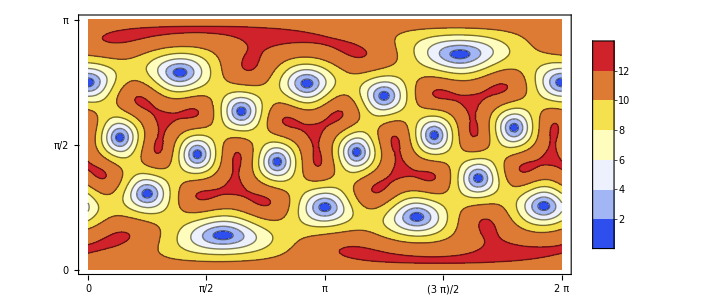

```mathematica
Show[cpMONOprelim[Tmat],FrameTicks->{Range[0,2π,π/2],Range[0,π,π/2]},AspectRatio->Automatic,ImageSize->600]
```

#### Plot on sphere.

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
If[$VersionNumber<12,
cpMONO[Tmat_]:=
Graphics3D[GraphicsComplex[xyzTP/@cpMONOprelim[Tmat][[1,1]], 
                                                                          cpMONOprelim[Tmat][[1,2]]]],
cpMONO[Tmat_]:=
Graphics3D[GraphicsComplex[xyzTP/@cpMONOprelim[Tmat][[1,1,1]], 
                                                                          cpMONOprelim[Tmat][[1,1,2]]]]];
```

```mathematica
Show[cpMONO[Tmat],Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Show[%,Lighting->{{"Ambient",White}}]
```

Thread::tdlen: Objects of unequal length in {{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«913»}],Polygon[{«298»}]}]]},{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«2377»}],Polygon[{«1055»}]}]]},{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«4002»}],Polygon[{«1696»}]}]]},{«1»},{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«7908»}],Polygon[{«2655»}]}]]},{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«8571»}],Polygon[{«2444»}]}]]},{Cos[EdgeForm[]],Cos[color],Cos[GraphicsGroup[{Polygon[{«3242»}],Polygon[{«1057»}]}]]}} {{},«7»,{}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«913»}],Polygon[{«298»}]}]]},{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«2377»}],Polygon[{«1055»}]}]]},{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«4002»}],Polygon[{«1696»}]}]]},{«1»},{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«7908»}],Polygon[{«2655»}]}]]},{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«8571»}],Polygon[{«2444»}]}]]},{Sin[EdgeForm[]],Sin[color],Sin[GraphicsGroup[{Polygon[{«3242»}],Polygon[{«1057»}]}]]}} {{},«7»,{}} cannot be combined.

-Graphics3D-

-Graphics3D-